# BoxPlot

```mathematica
importPath1=FileNameJoin[{$HomeDirectory,"Desktop","grafikdaten.xlsx"}];
importPath2=FileNameJoin[{$HomeDirectory,"Desktop","peanut wood.xlsx"}];

data=Import[importPath1][[1]];
data2=Import[importPath2][[1]];

labels=data[[1]];
labels2=data2[[1]];

data=data[[2;;]];
data2=data2[[2;;]];
```

```mathematica
dataTrans=Partition[Transpose[data],2]
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Grid[Transpose[]]

```mathematica
dataTrans2=Transpose[data2]
```

{{53.,32.,8.,8.,84.,9.,16.,60.,42.,8.,36.,18.,19.,12.,96.,14.,,},{46.,17.,125.,15.,16.,63.,127.,114.,20.,56.,41.,67.,64.,22.,23.,18.,20.,60.}}

```mathematica
datacopied={{{8.,31.,11.,9.,26.,14.,18.},{19.,11.,16.,9.,12.,25.,14.}},{{8.,8.,24.,10.,10.,16.,10.},{8.,8.,15.,25.,10.,9.,15.}},{{41.,60.,40.,51.,50.,30.,74.},{30.,37.,31.,41.,33.,80.,53.}},{{34.,22.,29.,25.,29.,31.,37.},{25.,20.,23.,45.,24.,29.,40.}}};
```

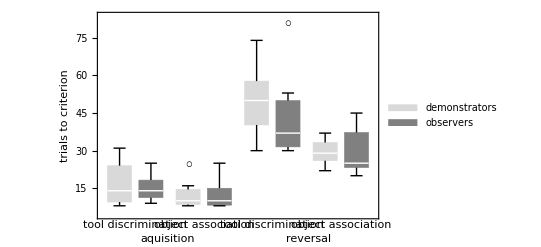

```mathematica
exportChart=Show[BoxWhiskerChart[datacopied,{"Outliers",
{"MedianMarker",1,Directive[Thick,White]},
{"Outliers","◦",Directive[FontSize->18,Black]},
{"FarOutliers","◦",Directive[Black]},
{"Whiskers",Thin},
{"Fences",Thin}},
BaseStyle->{FontFamily->"Arial",FontSize->14},
ChartLegends->Placed[{"demonstrators","observers"},{{Right,Top}},Style[#,FontFamily->"Arial",FontSize->14]&],
Frame->{True,True,None,None},
ChartBaseStyle->{EdgeForm[Thickness[.001]]},
ChartStyle->{LightGray,Gray},
BarSpacing->Small,
ChartElementFunction->"BoxWhisker",
Method->{"BoxRange"->(Quantile[#,Range[0,1,1/4],{{1/2, 0}, {0, 1}}]&)},
(*PlotLabel->"Whatever",*)
FrameLabel->{"","trials to criterion"},
Joined->False,
PlotRange->All,
ImageSize->Scaled[1],
ImageMargins->{{0,0},{60,0}}],
Graphics[Text["tool discrimination",Scaled@{.135,-0.03}]],
Graphics[Text["object association",Scaled@{.38,-0.03}]],
Graphics[Text[" tool discrimination",Scaled@{.62,-0.03}]],
Graphics[Text["object association",Scaled@{.865,-0.03}]],
Graphics[Text[Style["aquisition",Large],Scaled@{0.25,-0.1}]],
Graphics[Text[Style["reversal",Large],Scaled@{0.75,-0.1}]]
]
```

```mathematica
Export["theBigBoxes.eps",exportChart]
```

theBigBoxes.eps

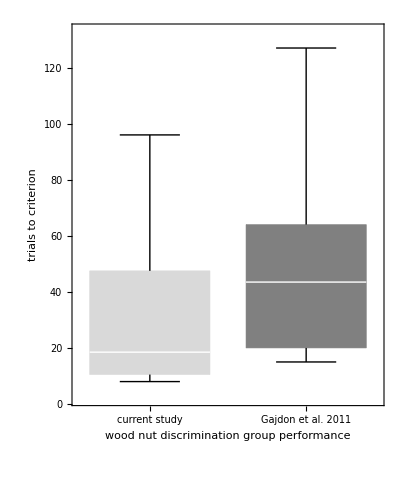

```mathematica
exportChart2=BoxWhiskerChart[{{53.,32.,8.,8.,84.,9.,16.,60.,42.,8.,36.,18.,19.,12.,96.,14.},{46.,17.,125.,15.,16.,63.,127.,114.,20.,56.,41.,67.,64.,22.,23.,18.,20.,60.}},{"Outliers",
{"MedianMarker",1,Directive[Thick,White]},
{"Outliers","◦",Directive[FontSize->18,Black]},
{"FarOutliers","◦",Directive[Black]},
{"Whiskers",Thin},
{"Fences",Thin}},
BaseStyle->{FontFamily->"Arial",FontSize->14},
(*ChartLegends->Placed[{"demonstrators","observers"},{{Right,Top}},Style[#,FontFamily->"Arial",FontSize->14]&],*)
Frame->{True,True,None,None},
ChartBaseStyle->{EdgeForm[Thickness[.001]]},
ChartLabels->{"current study","Gajdon et al. 2011"},
ChartStyle->{LightGray,Gray},
BarSpacing->Small,
Method->{"BoxRange"->(Quantile[#,Range[0,1,1/4],{{1/2, 0}, {0, 1}}]&)},
ChartElementFunction->"BoxWhisker",
FrameLabel->{Style["wood nut discrimination group performance",18],Style["trials to criterion",18]},
Joined->False,
PlotRange->All,
ImageMargins->{{0,0},{60,0}},
AspectRatio->1.2/1,
ImageSize->Scaled[1]]
```

```mathematica
Export["theBigBoxes2.eps",exportChart2]
```

```mathematica
"theBigBoxes2.eps"
```

theBigBoxes2.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["theBigBoxes.eps"]]]
```

## Diffenrent common quantile ranges:

```mathematica
ChartElementFunction["BoxWhiskerCharts"]
```

ChartElementFunction[BoxWhiskerCharts]

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{0, 0}, {1, 0}}]
```

{0.,0.2,0.5,0.8,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{0, 0}, {0, 1}}]
```

{0.,0.175,0.45,0.725,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1/2, 0}, {0, 0}}]
```

{0.,0.2,0.5,0.7,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1/2, 0}, {0, 1}}]
```

{0.,0.225,0.5,0.775,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{0, 1}, {0, 1}}]
```

{0.,0.2,0.5,0.8,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1, -1}, {0, 1}}]
```

{0.,0.25,0.5,0.75,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{1/3, 1/3}, {0, 1}}]
```

{0.,0.216667,0.5,0.783333,1.}

```mathematica
Quantile[Range[0,1,.1],Range[0,1,1/4],{{3/8, 1/4}, {0, 1}}]
```

{0.,0.21875,0.5,0.78125,1.}